# Embedding Space Geometry

## Rijksmuseum Semantic Explorer — Notebook 1 of 5

This project uses multilingual-e5-small, a sentence transformer that maps text (artwork titles, descriptions) into 384-dimensional vectors. These embeddings encode semantic meaning: similar artworks land nearby in this high-dimensional space. This notebook probes the geometry of that space itself — how is variance distributed across dimensions? What are typical inter-artwork distances? Does the space have exploitable low-dimensional structure? Understanding these geometric properties is essential background for the visualisations in the other notebooks, and reveals what the embedding model has learned about the Rijksmuseum collection.

## 1. Data Loading

The data was pre-exported from two SQLite databases using a Python bridge script (export_for_mathematica.py). Embeddings are stored as raw float32 binary: 20,000 artwork vectors, each 384 dimensions, totalling about 30 MB. Metadata is a JSON manifest containing artwork IDs, object numbers, titles, types, creators, subjects, materials, techniques, and dates. The embeddings were originally int8-quantized in the database and have been decoded to float32 and L2-normalised, so every vector has unit length. This normalisation means cosine similarity reduces to a simple dot product.

```mathematica
dataDir = FileNameJoin[{NotebookDirectory[], "data"}];
If[!DirectoryQ[dataDir],
  Print["Data not found. Run: uv run python export_for_mathematica.py"];
  Abort[]];

manifest = Import[FileNameJoin[{dataDir, "metadata.json"}], "RawJSON"];
{n, dim} = Lookup[manifest, {"n", "dim"}];
raw = BinaryReadList[FileNameJoin[{dataDir, "embeddings.bin"}], "Real32"];
embeddings = Partition[raw, dim];
artIds = manifest["art_ids"];
artworks = manifest["artworks"];
Print["Loaded ", n, " embeddings of dimension ", dim]
```

Loaded 20000 embeddings of dimension 384

## 2. Component Distributions

Each of the 384 embedding dimensions captures some aspect of an artwork's semantic content. By examining the marginal distribution of individual component values across all artworks, we can check for pathologies such as dead dimensions, extreme outliers, or heavy tails. For L2-normalised vectors from a sentence transformer, we expect roughly Gaussian component distributions centred near zero. The norm histogram serves as a sanity check: after normalisation, all norms should cluster tightly around 1.0, confirming that the data pipeline preserved the original geometry correctly.

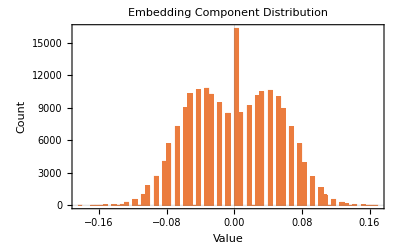
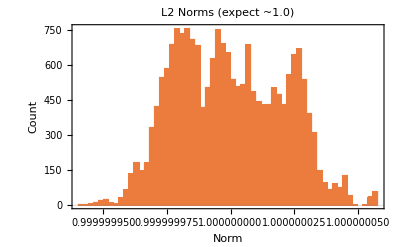

```mathematica
SeedRandom[42];
componentSample = RandomSample[Flatten[embeddings], Min[200000, n * dim]];

Row[{
  Histogram[componentSample, 100,
    PlotLabel -> "Embedding Component Distribution",
    AxesLabel -> {"Value", "Count"},
    PlotTheme -> "Scientific",
    ImageSize -> 400],
  Spacer[20],
  Histogram[Map[Norm, embeddings], 50,
    PlotLabel -> "L2 Norms (expect ~1.0)",
    AxesLabel -> {"Norm", "Count"},
    PlotTheme -> "Scientific",
    ImageSize -> 400]
}]
```

## 3. PCA Eigenspectrum

Principal Component Analysis decomposes the total variance of the embedding cloud into orthogonal directions (principal components), ranked from most to least informative. The eigenvalue of each component tells us how much variance it captures. A steep drop in the scree plot means a few directions dominate, and the data effectively lives on a lower-dimensional manifold — good news for dimensionality reduction methods like UMAP, which exploit this. The cumulative variance curve shows concretely how many components are needed to capture 50%, 80%, 90%, or 95% of the total variance, giving a practical measure of compressibility.

```mathematica
(* Center data and compute covariance matrix (384x384) *)
mu = Mean[embeddings];
centered = embeddings - ConstantArray[mu, n];
covMat = Transpose[centered].centered / (n - 1);

(* Eigensystem — real symmetric, so eigenvalues are real *)
{eigenvalues, eigenvectors} = Eigensystem[covMat];
order = Reverse[Ordering[eigenvalues]];
eigenvalues = eigenvalues[[order]];
eigenvectors = eigenvectors[[order]];
Print["Top 10 eigenvalues: ", eigenvalues[[1 ;; 10]] // NumberForm[#, 4] &]
```

Top 10 eigenvalues: {0.009685,0.007495,0.00569,0.004078,0.003821,0.003003,0.00283,0.002596,0.002511,0.002475}

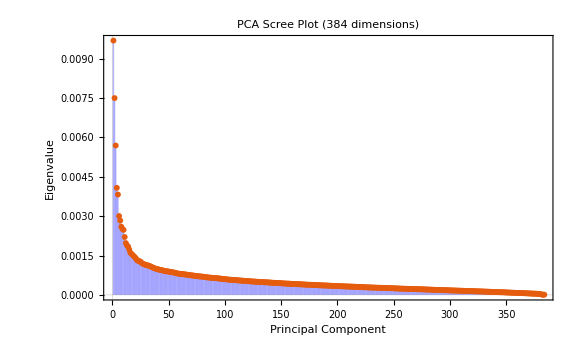

```mathematica
(* Scree plot *)
ListPlot[eigenvalues,
  PlotLabel -> "PCA Scree Plot (384 dimensions)",
  AxesLabel -> {"Principal Component", "Eigenvalue"},
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.3], Blue],
  PlotTheme -> "Scientific",
  PlotRange -> All,
  ImageSize -> Large]
```

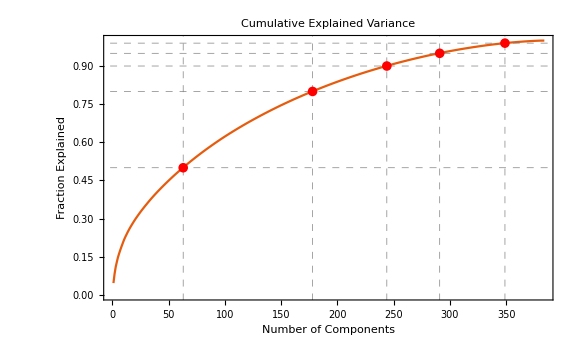

```mathematica
(* Cumulative explained variance *)
cumVar = Accumulate[eigenvalues] / Total[eigenvalues];

thresholds = {0.5, 0.8, 0.9, 0.95, 0.99};
nComponents = Table[LengthWhile[cumVar, # < t &] + 1, {t, thresholds}];

ListLinePlot[cumVar,
  PlotLabel -> "Cumulative Explained Variance",
  AxesLabel -> {"Number of Components", "Fraction Explained"},
  GridLines -> {nComponents, thresholds},
  GridLinesStyle -> Directive[Gray, Dashed],
  Epilog -> {PointSize[0.012], Red, Point[Thread[{nComponents, thresholds}]]},
  PlotTheme -> "Scientific",
  ImageSize -> Large]
```

```mathematica
(* Components needed for each variance threshold *)
Grid[
  Prepend[
    Transpose[{thresholds, nComponents}],
    Style[#, Bold] & /@ {"Variance Threshold", "Components Needed"}],
  Frame -> All, Alignment -> Center,
  Background -> {None, {LightBlue, {White}}}]
```

Variance Threshold | Components Needed
0.5 | 63
0.8 | 178
0.9 | 244
0.95 | 291
0.99 | 349

## 4. Effective Dimensionality

While the PCA eigenspectrum gives a full picture, it is useful to condense it into a single number. The participation ratio (PR) does this: it equals d when all d eigenvalues are equal (maximum spread) and 1 when all variance is concentrated in a single direction. We also compute an entropy-based dimensionality estimate using the Shannon entropy of the normalised eigenvalue distribution. Together these give a quick summary of how many dimensions are doing real work in representing the collection — often far fewer than the nominal 384.

```mathematica
(* Participation ratio: (Sum[lambda])^2 / Sum[lambda^2] *)
pr = Total[eigenvalues]^2 / Total[eigenvalues^2];
Print["Participation ratio: ", NumberForm[N[pr], 5]]
Print["Effective dimensionality: ~", Round[pr], " out of ", dim, " dimensions"]

(* Also compute via entropy *)
p = eigenvalues / Total[eigenvalues];
entropy = -Total[Select[p, # > 0 &] * Log[Select[p, # > 0 &]]];
entropyDim = Exp[entropy];
Print["Entropy-based dimensionality: ~", Round[entropyDim]]
```

Participation ratio: 117.47

Effective dimensionality: ~117 out of 384 dimensions

Entropy-based dimensionality: ~226

## 5. Pairwise Distance Distribution

The distribution of distances between random pairs of artworks characterises the overall geometry of the collection in embedding space. For L2-normalised vectors, cosine similarity is simply the dot product, and there is an exact algebraic relationship to Euclidean distance: ||a-b||^2 = 2(1-cos(a,b)), which we verify empirically. The shape of this distribution matters: a unimodal bell curve suggests a single diffuse cloud, while multimodality or long tails hint at cluster structure. Typical pairwise distances also set the scale for interpreting nearest-neighbor distances and cluster radii in later analyses.

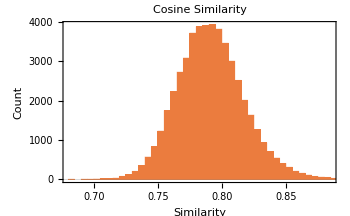
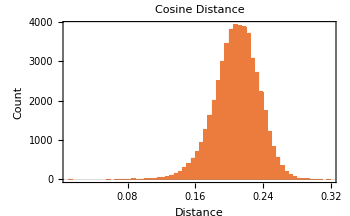
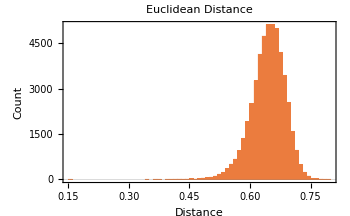

```mathematica
SeedRandom[42];
nPairs = 50000;
idx1 = RandomInteger[{1, n}, nPairs];
idx2 = RandomInteger[{1, n}, nPairs];
(* Avoid self-pairs *)
idx2 = MapThread[If[#1 == #2, Mod[#2, n] + 1, #2] &, {idx1, idx2}];

emb1 = embeddings[[idx1]];
emb2 = embeddings[[idx2]];
cosSims = Total[emb1 * emb2, {2}];
cosDists = 1 - cosSims;
eucDists = Sqrt[Total[(emb1 - emb2)^2, {2}]];

Row[{
  Histogram[cosSims, 80,
    PlotLabel -> "Cosine Similarity",
    AxesLabel -> {"Similarity", "Count"},
    PlotTheme -> "Scientific", ImageSize -> 350],
  Spacer[10],
  Histogram[cosDists, 80,
    PlotLabel -> "Cosine Distance",
    AxesLabel -> {"Distance", "Count"},
    PlotTheme -> "Scientific", ImageSize -> 350],
  Spacer[10],
  Histogram[eucDists, 80,
    PlotLabel -> "Euclidean Distance",
    AxesLabel -> {"Distance", "Count"},
    PlotTheme -> "Scientific", ImageSize -> 350]
}]
```

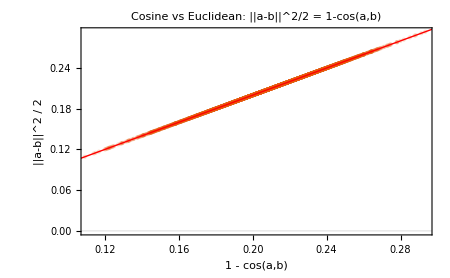

```mathematica
(* Verify the cosine-euclidean relationship *)
ListPlot[Transpose[{cosDists[[1 ;; 5000]], eucDists[[1 ;; 5000]]^2 / 2}],
  PlotLabel -> "Cosine vs Euclidean: ||a-b||^2/2 = 1-cos(a,b)",
  AxesLabel -> {"1 - cos(a,b)", "||a-b||^2 / 2"},
  PlotStyle -> Directive[PointSize[Tiny], Opacity[0.2]],
  PlotTheme -> "Scientific",
  Epilog -> {Red, Thick, Line[{{0, 0}, {1, 1}}]},
  ImageSize -> 450]
```

## 6. Nearest-Neighbor Analysis

While pairwise distances describe global geometry, nearest-neighbor distances reveal local structure — how dense is the embedding space around each artwork? We compute the distance from each artwork to its 1st, 5th, 10th, and 20th nearest neighbor. A narrow, symmetric distribution indicates roughly uniform density, while a wide or multimodal one signals that some artworks live in dense clusters while others are isolated. These k-NN distances are also directly relevant to UMAP and HDBSCAN, which rely on local neighborhood structure to build their low-dimensional representations and cluster assignments.

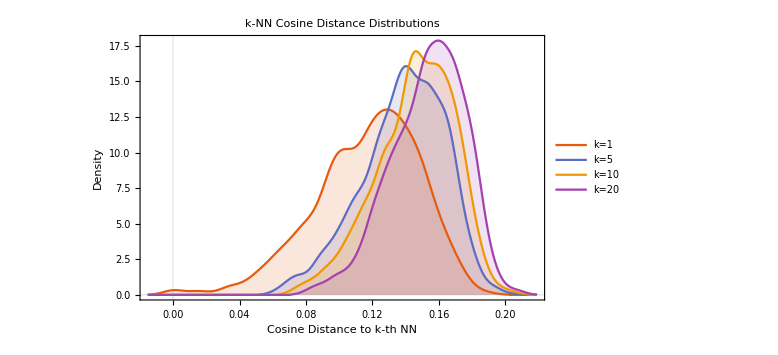

```mathematica
(* Subsample for pairwise computation *)
subN = Min[n, 2000];
SeedRandom[42];
subIdx = RandomSample[Range[n], subN];
subEmb = embeddings[[subIdx]];

(* Full cosine similarity matrix *)
simMat = subEmb.Transpose[subEmb];
Do[simMat[[i, i]] = -Infinity, {i, subN}]; (* mask self-similarity *)

(* k-NN distance distributions *)
kValues = {1, 5, 10, 20};
nnDists = Table[
  Table[1 - Sort[simMat[[i]], Greater][[k]], {i, subN}],
  {k, kValues}];

SmoothHistogram[nnDists,
  PlotLabel -> "k-NN Cosine Distance Distributions",
  AxesLabel -> {"Cosine Distance to k-th NN", "Density"},
  PlotLegends -> ("k=" <> ToString[#] & /@ kValues),
  Filling -> Axis, FillingStyle -> Opacity[0.15],
  PlotTheme -> "Scientific",
  ImageSize -> Large]
```

```mathematica
(* Median k-NN distances *)
Grid[
  Prepend[
    Transpose[{kValues, NumberForm[Median[#], 4] & /@ nnDists}],
    Style[#, Bold] & /@ {"k", "Median Distance"}],
  Frame -> All, Alignment -> Center]
```

k | Median Distance
1 | 0.1203
5 | 0.1407
10 | 0.1476
20 | 0.1551

## 7. 3D PCA Visualization

Projecting 384 dimensions down to three inevitably loses information, but the first three principal components capture the maximum possible variance in three orthogonal directions. This gives a rough overview of the embedding landscape, coloured by object type (e.g., print, painting, photograph). If types form visible clusters in this projection, it confirms that the embedding model has learned meaningful categorical distinctions. Note that PCA is a linear method, so it cannot reveal the nonlinear manifold structure that UMAP captures, but it does preserve global scale and relative distances faithfully.

```mathematica
(* Determine primary type per artwork *)
primaryTypes = Table[
  Module[{types = artworks[ToString[id]]["types"]},
    If[Length[types] > 0, First[types], "unknown"]],
  {id, artIds}];
topTypes = Keys[TakeLargest[Counts[primaryTypes], 8]];

(* Project all points onto first 3 PCs *)
pcBasis = eigenvectors[[1 ;; 3]];
projected3D = centered.Transpose[pcBasis];

(* One dataset per type *)
datasets3D = Table[Pick[projected3D, primaryTypes, type], {type, topTypes}];

ListPointPlot3D[datasets3D,
  PlotLegends -> topTypes,
  PlotStyle -> Table[Directive[PointSize[0.003], Opacity[0.4]], Length[topTypes]],
  BoxRatios -> {1, 1, 1},
  AxesLabel -> {"PC1", "PC2", "PC3"},
  PlotLabel -> "3D PCA Projection (colored by object type)",
  ViewPoint -> {2, -2.5, 1.5},
  ImageSize -> 700]
```

-Graphics3D-

## 8. Isotropy Analysis

An isotropic embedding space distributes vectors uniformly across the unit hypersphere, with no preferred direction. In practice, many transformer-based embeddings exhibit significant anisotropy: all vectors share a dominant mean direction, and the meaningful semantic variation happens in a subspace perpendicular to it. High anisotropy can reduce the effective discriminative power of cosine similarity, since all similarities get biased towards a high baseline. We measure this by computing each embedding's similarity to the global mean vector. If this distribution concentrates near a high value, the space is strongly anisotropic. The log-scale eigenvalue spectrum gives a complementary view: perfectly isotropic data would show a flat line.

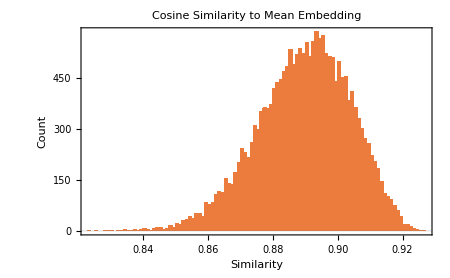
-Graphics-Mean pairwise cosine similarity: 0.7915
Std dev of pairwise cosine similarity: 0.02612
Mean similarity to centroid: 0.8897

Interpretation:
Highly anisotropic: embeddings cluster around a dominant direction.

```mathematica
(* Cosine similarity of each embedding to the global mean *)
meanEmb = Normalize[Mean[embeddings]];
cosToMean = embeddings.meanEmb;

Row[{
  Histogram[cosToMean, 80,
    PlotLabel -> "Cosine Similarity to Mean Embedding",
    AxesLabel -> {"Similarity", "Count"},
    PlotTheme -> "Scientific", ImageSize -> 450],
  Spacer[20],
  Column[{
    "Mean pairwise cosine similarity: " <> ToString[NumberForm[Mean[cosSims], 4]],
    "Std dev of pairwise cosine similarity: " <> ToString[NumberForm[StandardDeviation[cosSims], 4]],
    "Mean similarity to centroid: " <> ToString[NumberForm[Mean[cosToMean], 4]],
    "",
    Style["Interpretation:", Bold],
    If[Mean[cosToMean] > 0.5,
      "Highly anisotropic: embeddings cluster around a dominant direction.",
      If[Mean[cosToMean] > 0.2,
        "Moderately anisotropic: some directional bias.",
        "Relatively isotropic: embeddings spread across the sphere."]]
  }]
}]
```

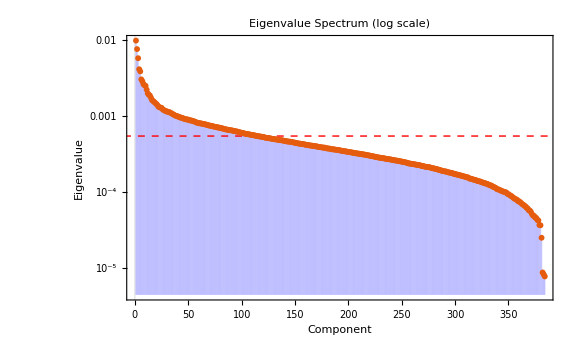

```mathematica
(* Eigenvalue spectrum shape — another isotropy indicator *)
(* For perfectly isotropic data, all eigenvalues would be equal *)
ListLogPlot[eigenvalues,
  PlotLabel -> "Eigenvalue Spectrum (log scale)",
  AxesLabel -> {"Component", "Eigenvalue"},
  PlotTheme -> "Scientific",
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.2], Blue],
  Epilog -> {Red, Dashed,
    InfiniteLine[{0, Log[Mean[eigenvalues]]}, {1, 0}]},
  ImageSize -> Large,
  PlotRange -> All]
```